```mathematica
mt =ImageData[-Graphics-//Binarize];
```

```mathematica
(*SplitBy 以全零行为条件分组，Flatten 又将分组还原成了原始矩阵*)
```

```mathematica
SplitBy[mtᵀ,MatchQ[#,{0..}]&]// Flatten[#,1]& // Transpose // ArrayPlot[#, ColorRules->{0->Black, 1->White}, Mesh->True] &
```

-Graphics-

```mathematica
SplitBy[mtᵀ,MatchQ[#,{0..}]&]/.{{x:Repeated[{0..},{1,1}]}:>({x}/.{0->2})} // Transpose/@#&;
```

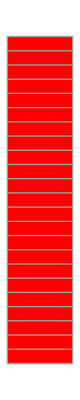
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
%// ArrayPlot[#, ColorRules->{0->Black, 1->White, _->Red}, Mesh->True] &  /@ # &
```

```mathematica
(*标记要保留的空白列*)
```

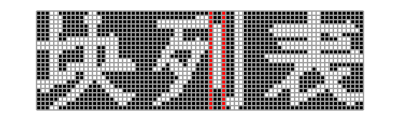

```mathematica
SplitBy[mtᵀ,MatchQ[#,{0..}]&]/.{{x:Repeated[{0..},{1,1}]}:>({x}/.{0->2})}// Flatten[#,1]& // Transpose // ArrayPlot[#, ColorRules->{0->Black, 1->White, 2->Red}, Mesh->True] &
```

```mathematica
SplitBy[mtᵀ,MatchQ[#,{0..}]&]/.{{x:Repeated[{0..},{1,1}]}:>({x}/.{0->2})}// Flatten[#,1]&; (*标记要保留的空白行*)
```

```mathematica
SplitBy[#,MatchQ[#,{0..}]&]/.{{0..}..}->Sequence[]& @ %;(*删除空白行*)
```

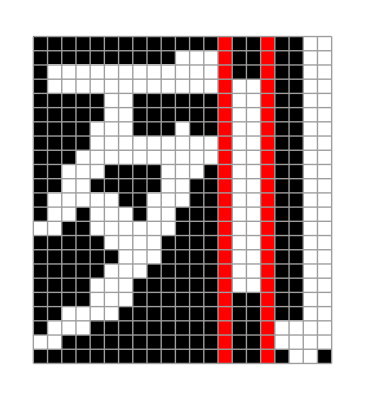
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
%//Transpose/@#&//ArrayPlot[#, ColorRules->{0->Black, 1->White, 2->Red}, Mesh->True] &/@#&
```

```mathematica
(*标记要保留的空白行*)
```

```mathematica
labelRowsPreserve[m_] :=SplitBy[mᵀ,MatchQ[#,{0..}]&]/.{{x:Repeated[{0..},{1,1}]}:>({x}/.{0->2})}// Flatten[#,1]&
```

```mathematica
(*删除空白行*)
```

```mathematica
delRowsBlank[m_]:=SplitBy[#,MatchQ[#,{0..}]&]/.{{0..}..}->Sequence[]& @m
```

```mathematica
splitZh[m_] :=m//labelRowsPreserve // delRowsBlank//#/.{x:2..}:>{x}/.{2->0}&//Transpose/@#&//ArrayPlot[#, ColorRules->{0->Black, 1->White, 2->Red}, Mesh->True] &/@#&
```

```mathematica
splitZh@mt
```

{-Graphics-,-Graphics-,-Graphics-}